```mathematica
Sum[x^k,{k,0,Infinity}]
```

1/(1-x)

Sum[x^k,{k,0,Infinity}]

WolframAlphaQueryResults

```mathematica
Re[1/(1-r/R Exp[I θ])]
```

Re[1/(1-(ⅇ^(ⅈ θ) r)/R)]

```mathematica
ExpToTrig[Re[1/(1-(ⅇ^(ⅈ θ) r)/R)]]
```

```mathematica
Re[1/(1-(r Cos[θ])/R-(ⅈ r Sin[θ])/R)//FullSimplify]//FullSimplify
```

Re[R/(-ⅇ^(ⅈ θ) r+R)]

```mathematica
ExpToTrig[Re[R/(-ⅇ^(ⅈ θ) r+R)]+1/2]
```

1/2+Re[R/(R-r Cos[θ]-ⅈ r Sin[θ])]

```mathematica
Re[R/(-ⅇ^(ⅈ θ) r+R)]+1/2//FullSimplify
```

1/2+Re[R/(-ⅇ^(ⅈ θ) r+R)]

```mathematica
ComplexExpand[-1/2+Re[R/(-ⅇ^(ⅈ θ) r+R)]]
```

-1/2+R^2/((R-r Cos[θ])^2+r^2 Sin[θ]^2)-(r R Cos[θ])/((R-r Cos[θ])^2+r^2 Sin[θ]^2)

```mathematica
TrigReduce[-1/2+R^2/((R-r Cos[θ])^2+r^2 Sin[θ]^2)-(r R Cos[θ])/((R-r Cos[θ])^2+r^2 Sin[θ]^2)]
```

```mathematica
(R^2-r^2 Cos[θ]^2-r^2 Sin[θ]^2)/(2 (R^2-2 r R Cos[θ]+r^2 Cos[θ]^2+r^2 Sin[θ]^2))//FullSimplify
```

(-r^2+R^2)/(2 (r^2+R^2-2 r R Cos[θ]))

```mathematica
TrigReduce[1+R^2/((R-r Cos[θ])^2+r^2 Sin[θ]^2)-(r R Cos[θ])/((R-r Cos[θ])^2+r^2 Sin[θ]^2)]
```

```mathematica
(2 R^2-3 r R Cos[θ]+r^2 Cos[θ]^2+r^2 Sin[θ]^2)/(R^2-2 r R Cos[θ]+r^2 Cos[θ]^2+r^2 Sin[θ]^2)//FullSimplify
```

(r^2+2 R^2-3 r R Cos[θ])/(r^2+R^2-2 r R Cos[θ])

```mathematica
(3 R^2-4 r R Cos[θ]+r^2 Cos[θ]^2+r^2 Sin[θ]^2)/(2 (R^2-2 r R Cos[θ]+r^2 Cos[θ]^2+r^2 Sin[θ]^2))//FullSimplify
```

(r^2+3 R^2-4 r R Cos[θ])/(2 (r^2+R^2-2 r R Cos[θ]))

```mathematica
$Assumptions={Abs[r]≤1,n∈Integers}
```

{Abs[r]≤1,n∈ℤ}

```mathematica
∫_0^(2Pi) (1-r^2)/(1+r^2-2r Cos[θ])Exp[I θ ω]ⅆθ
```

$Aborted

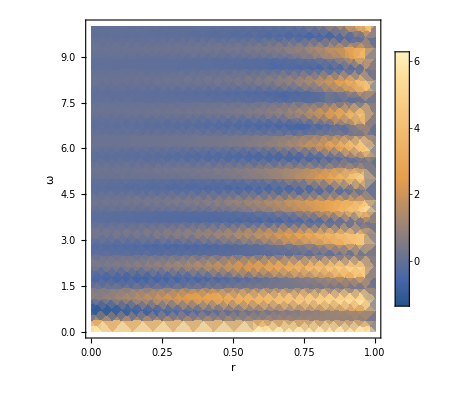

```mathematica
DensityPlot[NIntegrate[(1-r^2)/(1+r^2-2r Cos[θ])Cos[ θ ω],{θ,0,2Pi}],{r,0,1},{ω,0, 10},PerformanceGoal->"Quality",PlotLegends->Automatic,FrameLabel->Automatic]
```

```mathematica
∫_0^(2Pi) (Sin[(n+1/2)x])^2ⅆx
```

π

```mathematica
∫_0^(2Pi) Sin[(n+1/2)x]/Sin[x/2] ⅆθ
```